```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ResourceFunction["ExportRotatingGIF"]
```

```mathematica
exp[x_,y_,z_]=Exp[-Sqrt[(x^2+y^2+z^2)]];RealSphericalHarmonic[l_,m_,θ_,ϕ_]=Piecewise[{{√2(-1)^m Im[SphericalHarmonicY[l,Abs[m],θ,ϕ]],m>0},{SphericalHarmonicY[l,m,θ,ϕ],m==0},{√2(-1)^m Re[SphericalHarmonicY[l,m,θ,ϕ]],m<0}}];
CartesianSphericalHarmonic[l_,m_,x,y,z]=RealSphericalHarmonic[l,m,ToSphericalCoordinates[{x,y,z}][[2]],ToSphericalCoordinates[{x,y,z}][[3]]];
s[x_,y_,z_]=1/(2 √π);
px[x_,y_,z_]=(√(3/π) x)/(2 √(x^2+y^2+z^2)) ;
py[x_,y_,z_]=(√(3/π) y)/(2 √(x^2+y^2+z^2)) ;
pz[x_,y_,z_]=(√(3/π) z)/(2 √(x^2+y^2+z^2)) ;
orbital[expr_]=Abs[expr]expr exp[x,y,z];
```

```mathematica
Options[plotContours]={"PositiveColor"->Red,"NegativeColor"->Blue};
plotContours[expr_,lim_,range_,OptionsPattern[]]:=ContourPlot3D[Quiet[(expr Abs[expr])/(√(x^2+y^2+z^2))],{x,-range,range},{y,-range,range},{z,-range,range},Contours->{{lim,Directive[OptionValue["PositiveColor"],Opacity[0.7]]},{-lim,Directive[OptionValue["NegativeColor"],Opacity[0.7]]}},Mesh->None]
```

```mathematica
plotContours[px[x,y,z],0.5,2]
```

-Graphics3D-

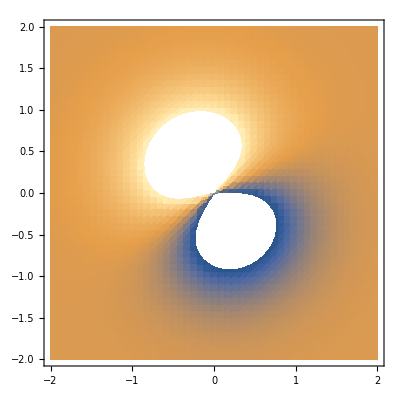

```mathematica
DensityPlot[1/(√3)s[x,y,0]-1/(√6)px[x,y,0]+1/(√2)py[x,y,0],{x,-2,2},{y,-2,2},PlotPoints->50]
```

```mathematica
plotContours[1/(√3)s[x,y,z]+√(2/3)px[x,y,z],0.1,4,"PositiveColor"->Magenta,"NegativeColor"->Green]
```

$Aborted

```mathematica
sp2=Show[plotContours[1/(√10)s[x,y,z]-1/(√6)px[x,y,z]+1/(√2)py[x,y,z],0.11,4,"PositiveColor"->Magenta,"NegativeColor"->Green],plotContours[1/(√10)s[x,y,z]-1/(√6)px[x,y,z]-1/(√2)py[x,y,z],0.11,4,"PositiveColor"->Magenta,"NegativeColor"->Green],plotContours[1/(√10)s[x,y,z]+√(2/3)px[x,y,z],0.11,4,"PositiveColor"->Magenta,"NegativeColor"->Green],plotContours[pz[x,y,z],0.11,4]]
```

-Graphics3D-

```mathematica
Show[sp2,ViewPoint->{3Cos[1 π/20],3Sin[1 π/20],0.75},Boxed->False,Axes->None]
```

-Graphics3D-

```mathematica
["test.gif",Graphics3D[sp2[[1]]],"Graphics3DOptions"->{Boxed->False,Axes->None,ImageSize->{1920,1080}},"InitialViewPoint"->{0,3,0.75},"Axis"->"z"]
```

test.gif

```mathematica
rotating=Table[Graphics3D[GeometricTransformation[sp2[[1]],RotationTransform[n π/20,{0,0,1}]],Boxed->False,Axes->None,PlotRange->{{-4,4},{-4,4},{-4,4}},ViewPoint->{3,0,0.75}],{n,0,40}];
```

```mathematica
rotating[[1]]
```

-Graphics3D-

```mathematica
Molecule["silicon"]
```

Molecule[…]

```mathematica
Export["test.mp4",rotating,RasterSize->{1920,1080},Background->Black]
```

test.mp4

```mathematica
Graphics3D[GeometricTransformation[sp2[[1]],RotationTransform[0.1,{0,0,1}]]]
```

-Graphics3D-

```mathematica
Graphics3D[GeometricTransformation[sp2[[1]],RotationTransform[0.1,{0,0,1}]],Boxed->False,Axes->None,,PlotRange->{{-4,4},{-4,4},{-4,4}}]
```

-Graphics3D-

```mathematica
AnimationVideo[Graphics3D[GeometricTransformation[sp2[[1]],RotationTransform[a,{0,0,1}]],Boxed->False,Axes->None,PlotRange->{{-4,4},{-4,4},{-4,4}}],{a,0,2π,2 π/20},RasterSize->{1920,1080}]
```

```mathematica
ListAnimate[rotating]
```

```mathematica
E
```

```mathematica
plotContours[1/(√3)s[x-2+t/10,y,z]-1/(√6)px[x-2+t/10,y,z]+1/(√2)py[x-2+t/10,y,z]]
```

```mathematica
plotContours[px[x,y,z],0.2,2]
```

-Graphics3D-

```mathematica
TrigReduce[SphericalHarmonicY[1,0,ToSphericalCoordinates[{x,y,z}][[1]],ToSphericalCoordinates[{x,y,z}][[2]]]]
```

```mathematica
RealSphericalHarmonic[l_,m_,θ_,ϕ_]=Piecewise[{{√2(-1)^m Im[SphericalHarmonicY[l,Abs[m],θ,ϕ]],m>0},{SphericalHarmonicY[l,m,θ,ϕ],m==0},{√2(-1)^m Re[SphericalHarmonicY[l,m,θ,ϕ]],m<0}}];
```

```mathematica
ContourPlot3D[(Quiet@Re[SphericalHarmonicY[1,1,ToSphericalCoordinates[{x,y,z}][[2]],ToSphericalCoordinates[{x,y,z}][[3]]]])^2 s[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Contours->{{0.1,Red},{-0.1,Blue}}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Abs[1/(√6)RealSphericalHarmonic[1,-1,θ,ϕ]+1/(√3)RealSphericalHarmonic[0,0,θ,ϕ]+1/(√2)RealSphericalHarmonic[1,0,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π},PlotRange->All]
```

-Graphics3D-

```mathematica
Show[plotContours[px[x,y,z],0.2,2]]
```

-Graphics3D-

```mathematica
graphs=Table[plotContours[z s[x+2-t/10,y,z]+z s[x-2+t/10,y,z],0.05,4],{t,0,10}];
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
RegionPlot3D[Abs[1/(√10)s[x,y,z]+1/(√6)px[x,y,z]+1/(√2)py[x,y,z]]>0.2,{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
increaseNegative[expr_]=Piecewise[{{expr, expr>0},{expr,True}}];
```

```mathematica
Show[plotContours[1/(√3)s[x,y,z]+1/(√6)px[x,y,z]+1/(√2)py[x,y,z],0.6,1.5,"PositiveColor"->Green],plotContours[1/(√3)s[x,y,z]+1/(√6)px[x,y,z]-1/(√2)py[x,y,z],0.6,1.5,"PositiveColor"->Green],plotContours[increaseNegative[1/(√3)s[x,y,z]-√(2/3)px[x,y,z]],0.6,1.5,"PositiveColor"->Green],plotContours[pz[x,y,z],0.33,1.5]]
```

-Graphics3D-

```mathematica
ContourPlot3D[z s[x+2Cos[π/3],y+2Sin[π/3],z]+z s[x+2Cos[π/3],y-2Sin[π/3],z]+ z s[x,y,z],{x,-4.,4.},{y,-4.,4.},{z,-4.,4.},Contours->{{.1,Red},{-.1,Blue}}]
```

```mathematica
ContourPlot3D[Sum[z s[x+2Cos[n π/3],y+2Sin[n π/3],z],{n,1,6}],{x,-4.,4.},{y,-4.,4.},{z,-4.,4.},Contours->{{.1,Directive[Red,Opacity[0.7]]},{-.1,Directive[Blue,Opacity[0.7]]}},MaxRecursion->1,PlotPoints->5,Mesh->None]
```

-Graphics3D-

```mathematica
px=ContourPlot3D[s[x,y,z]+x s[x,y,z]+y s[x,y,z]+z s[x,y,z],{x,-3.,3.},{y,-3.,3.},{z,-3.,3.},Contours->{{.04,Red},{-.04,Blue}},PlotPoints->5]
```

-Graphics3D-

```mathematica
Solve[s[x,y,z]+x s[x,y,z]+y s[x,y,z]+z s[x,y,z]==1/2,{x,y,z}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ⅇ^(-x^2-y^2-z^2)+ⅇ^(-x^2-y^2-z^2) x+ⅇ^(-x^2-y^2-z^2) y+ⅇ^(-x^2-y^2-z^2) z==1/2,{x,y,z}]

```mathematica
Export[NotebookDirectory[]<>"test.obj",DiscretizeGraphics[px]]
```

/Users/zimingqiu/PycharmProjects/ChemPresentation/test.obj

```mathematica
Mesh
```

```mathematica
px=ContourPlot3D[s[x,y,z]-x s[x,y,z]+y s[x,y,z]+z s[x,y,z],{x,-3.,3.},{y,-3.,3.},{z,-3.,3.},Contours->{{.04,Red},{-.04,Blue}},PlotPoints->5]
```

-Graphics3D-

```mathematica
px=ContourPlot3D[s[x,y,z]+x s[x,y,z]-y s[x,y,z]-z s[x,y,z],{x,-3.,3.},{y,-3.,3.},{z,-3.,3.},Contours->{{.04,Red},{-.04,Blue}},PlotPoints->5]
```

-Graphics3D-

```mathematica
px=ContourPlot3D[s[x,y,z]-x s[x,y,z]-y s[x,y,z]+z s[x,y,z],{x,-3.,3.},{y,-3.,3.},{z,-3.,3.},Contours->{{.04,Red},{-.04,Blue}},PlotPoints->5]
```

-Graphics3D-

```mathematica
px=ContourPlot3D[s[x,y,z]-x s[x,y,z]+y s[x,y,z]-z s[x,y,z],{x,-3.,3.},{y,-3.,3.},{z,-3.,3.},Contours->{{.04,Red},{-.04,Blue}},PlotPoints->5]
```

-Graphics3D-